# Resonant Mode-Mixing Last Updated: 1/31/2021

```mathematica
Remove["Global`*"]
```

## 1 Find resonances

## 1.1 Get normal mode data

```mathematica
m=m0*{1,a};(*Enter chain configuration here: 1 is lower mass ion, a is higher mass ion*)
Num =Length[m];wmhz=2*Pi*1*^6;
kM =Append[ Array[k,{2,2}],{kz,kz}];kM=Transpose[Table[If[m[[i]]===m0,kM[[1;;,1]],kM[[1;;,2]]],{i,Num}]];xM = Array[x,{3,Num}];
		(*1.1.2 Calculate Equilibrium Positions (axial crystal)*)
z0M = Array[z0,Num];
L0EQ [i_]:=z0M[[i]]==(Sum[(z0M[[i]] - z0M[[k]])^(-2),{k,1,i-1}] - Sum[(z0M[[i]] - z0M[[k]])^(-2),{k, i+1,Num}])
L0EQlist = Table[L0EQ[i],{i,Num}] //FullSimplify;z0M=z0M/.NSolve[L0EQlist,z0M, Reals][[1]];
L0Mn[i_,j_,n_]:=If[i==j,0,Abs[z0M[[i]]-z0M[[j]]]^n]
		(*1.1.3 Create matrix & find eigen*)
ke2=2.306569*^-28;l0=(ke2/kz)^(1/3);
ics=ArrayReshape[Append[Table[xM[[d,i]]->0,{d,2},{i,Num}],Table[(xM[[3,i]]-xM[[3,j]])->L0Mn[i,j,1]*l0,{i,Num},{j,i+1,Num}]],{Num*(Num+3)/2}];
Uel=Total[0.5*kM*(xM^2),2]+ke2*Sum[(Total[(xM[[;;,i]]-xM[[;;,j]])^2])^(-0.5),{i,Num},{j,i+1,Num}];
Vel1=-Table[D[Uel,{xM[[d,i]]},{xM[[d,j]]}]/Sqrt[m[[i]]*m[[j]]],{d,3},{i,Num},{j,Num}]/.ics//FullSimplify;
		(*1.1.4 Subbing in secular frequency expressions*)
k[1,1]=U*(3.25*^-40/m0*α/r0^4-1.602*^-13*κ/z0^2)//FullSimplify;k[2,1]=k[1,1];
k[1,2]=U*(3.25*^-40/a/m0*α/r0^4-1.602*^-13*κ/z0^2)//FullSimplify;k[2,2]=k[1,2];
kz=3.204*^-13*κ*U/z0^2//FullSimplify;
		(*1.1.5 Subbing in values*)
a=1.4;m0=40*1.66054*^-27;κ=1;(*Enter mass values here: a is mass ratio (>1), m0 is mass of smaller ion*)
r0=0.2;z0=0.4;(*Enter trap parameters here: r0 is radial ion-electrode distance (in mm), z0 is axial ion-electrode distance (in mm)*)
αmin=1.479*^27*a*m0*r0^4/z0^2;
		(*1.1.6 Get eigen*)
eigenholder=Table[Eigensystem[Vel1[[d]]],{d,3}];
wmlist=Sqrt[-eigenholder[[;;,1]]]/wmhz//FullSimplify;vlist=eigenholder[[;;,2]]//FullSimplify;
```

## 1.2 Calculate resonances

```mathematica
resSolnsp=Table[{{i,j,k},NSolve[{wmlist[[3,i]]==wmlist[[1,j]]+wmlist[[1,k]]/.{U->1},α>αmin},α,PositiveReals]},{i,Num},{j,Num},{k,j}]
resSolnsm=Table[{{i,j,k},NSolve[{wmlist[[3,i]]==wmlist[[1,j]]-wmlist[[1,k]]/.{U->1},α>αmin},α,PositiveReals]},{i,Num},{j,2,Num},{k,j-1}]
```

{{{{{1,1,1},{{α→6.03829}}}},{{{1,2,1},{{α→4.61278}}},{{1,2,2},{{α→3.0459}}}}},{{{{2,1,1},{{α→4.49651}}}},{{{2,2,1},{}},{{2,2,2},{{α→1.83177}}}}}}

{{{{{1,2,1},{{α→101.917}}}}},{{{{2,2,1},{{α→3.83137},{α→31.8576}}}}}}

```mathematica
AllTrue[ArrayReshape[wmlist/.{U->1}/.resSolnsp[[1,2,1,2]],3*Num],Im[#]==0&]
```

True

## 2 Get evolution of state

## 2.1 Calculate interaction matrix

```mathematica
nx={1,2};nz={2,3};(*Enter initial mode populations*)
resModes={1,2,1};(*Enter resonance modes*)
resDir={-1,-1,1};(*Enter resonance directions*)
Vnm0=20000;(*Enter base coupling strength here*)

a1=Abs[Min[If[resDir[[1]]==resDir[[2]],-1,1]*{nx[[resModes[[1]]]],nx[[resModes[[2]]]]}*resDir[[;;2]]]];
a2=Abs[Max[If[resDir[[1]]==resDir[[2]],-1,1]*{nx[[resModes[[1]]]],nx[[resModes[[2]]]]}*resDir[[;;2]]]];
g1=nz[[resModes[[3]]]];
rng=If[resDir[[1]]==resDir[[2]],g1,Min[a2,g1]];rng1=If[resDir[[1]]==resDir[[2]],a2,Max[a2,g1]];
ics=ConstantArray[0,a1+rng+1];ics[[g1+1-If[resDir[[1]]==resDir[[2]],0,Abs[a1-rng1]]]]=1;

nval=Sqrt[Reverse[Range[a1+rng]]*Range[a1+rng]*(If[resDir[[1]]==resDir[[2]],Reverse[Range[a1+rng]],Range[a1+rng]]+Abs[a1-rng1])];
Vnm=-I*Vnm0*(DiagonalMatrix[nval,1]+DiagonalMatrix[nval,-1]);
ln=N[Eigenvalues[Vnm]];vn=N[Eigenvectors[Vnm]];vn=Table[Normalize[vn[[i]]],{i,a1+rng+1}];

Cnm=Chop[((Inverse[Transpose[vn]].ics)*Exp[ln*t]).vn]//FullSimplify;
{Range[0,a1+rng],Reverse[Range[0,a1+rng]],If[resDir[[1]]==resDir[[2]],Reverse[Range[0,a1+rng]],Range[0,a1+rng]]+Abs[a1-rng1]};
nAvg=Table[Total[Abs[Cnm]^2*%[[i]]],{i,3}];
```

## 2.2 Plot state populations

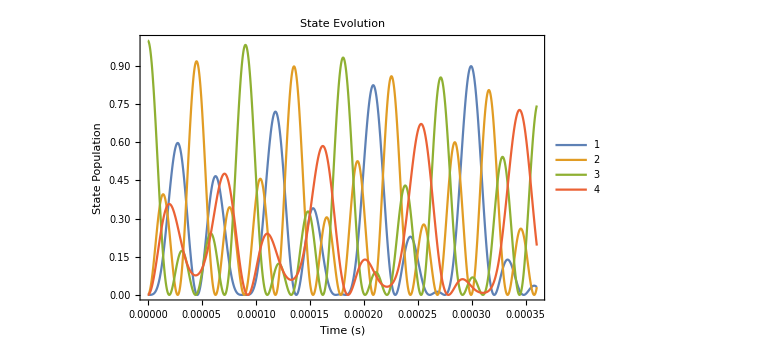
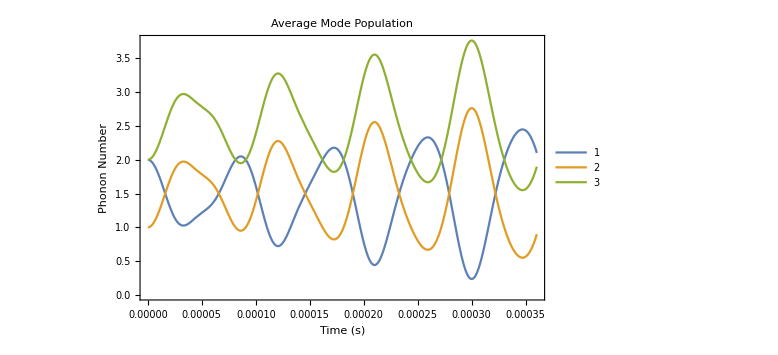

```mathematica
tmax=6*2*Pi/Max[Abs[ln]];
{Plot[Evaluate[Abs[Cnm[[]]]^2],{t,0,tmax},PlotLegends->Automatic,ImageSize->Large,Frame->True,PlotLabel->"State Evolution",FrameLabel->{"Time (s)","State Population"},PlotRange->{{0,tmax},{0,1}}],Plot[Evaluate[nAvg],{t,0,tmax},PlotLegends->Automatic,ImageSize->Large,Frame->True,PlotLabel->"Average Mode Population",FrameLabel->{"Time (s)","Phonon Number"}]}
```

## 3 Simulate cooling

## 3.1 Base functions

```mathematica
PDFfunct[xd_,Cnmd_,a1d_,rngd_]:=Piecewise[Table[{Abs[Cnmd[[i+1]]]^2,xd==i},{i,0,a1d+rngd}]];
heat[state_]:=state-If[AllTrue[state-{0,1,0},#>0&],{0,1,0},0];

rmmSimulate[state_,empty_]:=Module[{a1,a2,g1=state[[3]],a1ind,a2ind,rng,rng1,ics,nval,Vnm,ln,vn,Cnm,randN,tmix,newstate={0,0,0}},
a1=Abs[Min[If[resDir[[1]]==resDir[[2]],-1,1]*{state[[1]],state[[2]]}*resDir[[;;2]]]];a1ind=Position[state,a1][[1,1]];
a2=Abs[Max[If[resDir[[1]]==resDir[[2]],-1,1]*{state[[1]],state[[2]]}*resDir[[;;2]]]];a2ind=Position[state,a2][[1,1]];
rng=If[resDir[[1]]==resDir[[2]],g1,Min[a2,g1]];rng1=If[resDir[[1]]==resDir[[2]],a2,Max[a2,g1]];
ics=ConstantArray[0,a1+rng+1];ics[[g1+1-If[resDir[[1]]==resDir[[2]],0,Abs[a1-rng1]]]]=1;
nval=Sqrt[Reverse[Range[a1+rng]]*Range[a1+rng]*(If[resDir[[1]]==resDir[[2]],Reverse[Range[a1+rng]],Range[a1+rng]]+Abs[a1-rng1])];
Vnm=-I*Vnm0*(DiagonalMatrix[nval,1]+DiagonalMatrix[nval,-1]);
ln=N[Eigenvalues[Vnm]];vn=N[Eigenvectors[Vnm]];vn=Table[Normalize[vn[[i]]],{i,a1+rng+1}];
tmix=RandomReal[{1.*^-3,1*^-2}];
Cnm=Chop[((Inverse[Transpose[vn]].ics)*Exp[ln*tmix]).vn]//FullSimplify;
randN=RandomVariate[ProbabilityDistribution[PDFfunct[x,Cnm,a1,rng],{x,0,a1+rng,1}]];
newstate[[a1ind]]=a1+rng-randN;newstate[[a2ind]]=If[resDir[[1]]==resDir[[2]],a1+rng+Abs[a1-rng1]-randN,If[g1>a2,randN,Abs[a1-rng1]+randN]];newstate[[3]]=randN+If[resDir[[1]]≠resDir[[2]]&&g1>a2,Abs[a1-rng1],0];
heat[newstate]
]
```

## 3.2 Simulate!

```mathematica
iterations=20;
system=FoldList[rmmSimulate,{nx[[resModes[[1]]]],nx[[resModes[[2]]]],nz[[resModes[[1]]]]},Range[iterations]];
```

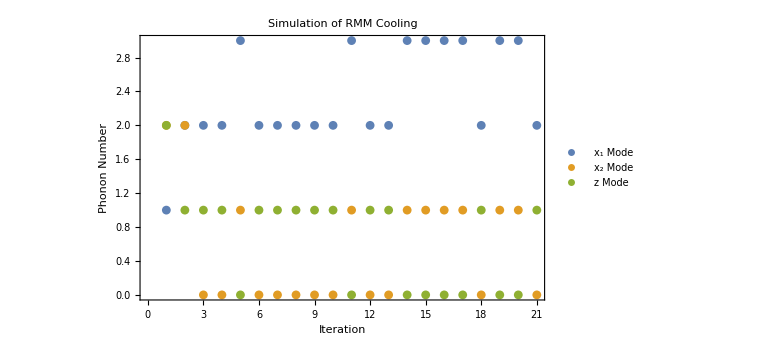

```mathematica
ListPlot[Transpose[system],PlotLabel->"Simulation of RMM Cooling",ImageSize->Large,PlotLegends->{"x_1 Mode","x_2 Mode","z Mode"},Frame->True,FrameLabel->{"Iteration","Phonon Number"}]
```